## Introduction to Neural Networks Daniel Kersten

## Problem Set 2

Prove that a linear neuron can be interpreted as a “template” matcher. (No programming needed. Just a sentence or two.)

Let  w be a weight vector representing a template pattern. You can think of w as representing the strengths of a set of synapses to a neuron. Let {x} be a collection of input pattern vectors all of unit length (norm).  The values of the elements of x represent the strengths of the inputs to the neuron. Show theoretically that the dot product of  x with w gives maximum response to the pattern x’ that matches the "form" of the template pattern. This is the basis for thinking of a neuron with receptive field w as being “selective” for a feature--a “feature detector”-- with inputs of the same form as the weights.

Goal: show that the dot product of x with w gives maximum response to the pattern x’ that matches the “form” of the template pattern (w).
Answer:
By definition, x . w = ||x|| || w|| cos(theta), where theta = the angle between x and w. Since ||x|| = 1, x . w = ||w|| cos(theta). We would like to find the x’ that maximizes “x . w”, so we can remove the ||w|| term as it is constant over all possible values of x. Thus, the argmax (over x) of “x . w” is equivalent to the argmax (over x) of “cos(theta)”. Thus, “x.w” is maximized when x lies in the same direction as w (theta = 0, so cos(theta) = 1, maximized). When x lies in the same direction as w, x is just the unit directional vector of w, thus “matching the form” of the template pattern w.

Derivative practice

This exercise will give you some more practice with the symbolic processing in Mathematica. Later on, when we study multiple layer perceptrons we will use the derivative of a non-linear squashing function in our derivation of the back-propagation learning rule. For this reason, it is useful to have a squashing function that is differentiable. It is also useful to have a closed form solution for the derivative.

a) Use Mathematica to take the derivative of the logistic function, squash[r_] := 1/(1 + Exp[-r/.25]);
Then use the output to define a function dsquash[]. Plot dsquash from r = -2 to 2.  (Tip: There are a number of ways to specify dsquash[]. Depending on how you do it, you may need to use the Evaluate[] function. )

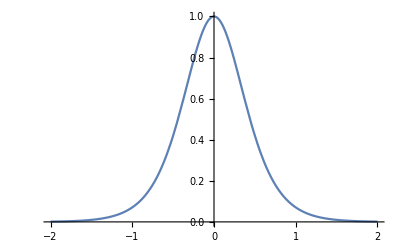

```mathematica
squash[r_] := 1/(1 + Exp[-r/.25])
dsquash[r_] := squash'[r]
Plot[dsquash[r], {r, -2, 2}]
```

b) Mathematica has a built-in function: LogisticSigmoid[ ]. Use D[ ], but this time compute the derivative of LogisticSigmoid[r]. This exercise illustrates a particularly nice property of the logistic function, that its derivative is a simple quadratic function of  it.

```mathematica
D[LogisticSigmoid[r], r]
```

(1-LogisticSigmoid[r]) LogisticSigmoid[r]

Projection and the successive approximation of a signal

The response of single model neuron in a population can be viewed as "the projection" of the input onto the basis vector represented by that neuron's receptive field weights. With respect to reconstruction, a basis set can be over- or under-complete. An over-complete set can be useful for sparse coding, where relatively few neurons are required to represent an otherwise high-dimensional input. This kind of code is efficient in spiking activity, but inefficient in the number of neurons required. An under-complete set can also be useful to capture the smaller dimensional space occupied by a set of interest (e.g. the set of “faces” or “natural sounds”). This kind of code could be efficient in the reducing the number of neurons, but they may all have to be active to accurately represent the input. This latter approach is related to “dimensionality reduction” methods. We’ll cover this in more detail later. 

The idea behind this exercise is that we can often get a good approximation to signal, or better, good approximations on average over a particular ensemble with only a subset of some assumed complete basis set.

The exercise illustrates how we can get better approximations of particular inputs by adding more “features”, i.e. basis vectors, from the Walsh set. This is the same idea behind Fourier synthesis, where a signal (sound or image) can be reconstructed with increasing accuracy by adding more and more sine waves of increasingly higher frequencies. 

In addition, the exercise illustrates how the the quality of the approximation depends on how well the basis set “fits” the signals being approximated.

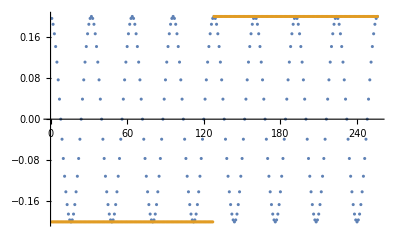

```mathematica
vsize = 256;
walshsetmatrix=HadamardMatrix[vsize ]; 
cossetmatrix=N@FourierDCTMatrix[vsize];
edge = Table[.4*UnitStep[x-vsize/2]-.2,{x,1,vsize }];
cos = Table[.2*(Cos[x*2.*Pi/(vsize/8)]),{x,1,vsize }];
ListPlot[{cos,edge}]
```

a) Compute and plot the spectra of edge and cos, with respect to the  basis vectors in cossetmatrix. 
Call them edgespectrum  and cosspectrum, respectively.

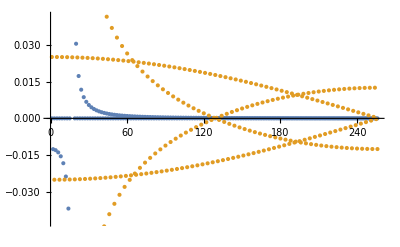

```mathematica
edgespectrum= edge.cossetmatrix;
cosspectrum = cos.cossetmatrix;
ListPlot[{cosspectrum ,edgespectrum}]
```

b) Using one line of code, use: ListPlot, Total, Projection[edge,#]&, and /@ to show that one can reconstruct edge and cos by summing up the projections of edge  onto each row of walshsetmatrix. Do the same for cos as input. 
Your output should look something like this:

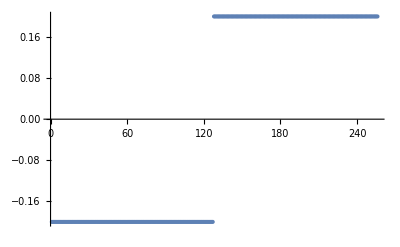

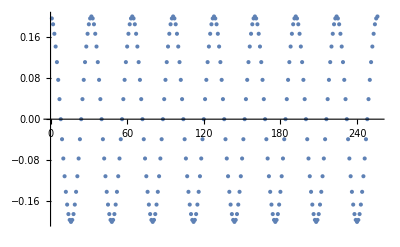

```mathematica
ListPlot[{Total[Projection[edge, #]& /@ walshsetmatrix, 1]}]
ListPlot[{Total[Projection[cos, #]& /@ walshsetmatrix, 1]}]
```

c) Now show that you don’t need all of the basis vectors to get good approximations of edge and cos using the walsh set.  Do this by adapting your expression in the previous answer to act as an argument for Manipulate[], together with a slider for parameter nn which indexes the rows of walshsetmatrix[[1;;nn,All]] . 

The figure below shows a sample output for nn =32 basis vectors to approximate the cos vector.

Tip: In Manipulate, in addition to sliders, you can also have buttons, such as sigtype= “edge” or “cos”. And you can use ToExpression@sigtype, to convert a string to an expression. To see what it does try executing: ToExpression@“edge”

To get a graph like the above you can use: Manipulate[ListPlot[{?[??[ToExpression@sigtype,#]&/@???,ToExpression@sigtype},Joined→True],{nn,1,vsize,1},{sigtype,{“edge”,”cos”}}], with the ?,??,??? marks filled in

```mathematica
Manipulate[ListPlot[{Total[Projection[ToExpression@sigtype,#]&/@walshsetmatrix[[1;;nn,All]], 1],ToExpression@sigtype},Joined->True],{nn,1,vsize,1},{sigtype,{"edge","cos"}}]
```

d) In the last exercise replace walshsetmatrix with cossetmatrix in your answer to c. Note that as you add increasing number of cosines waves to fit the edge, you observe “ringing” -- a  classic effect called the “Gibbs phenomenon”. 

One intuition for using periodic basis functions that are ordered from low to high frequencies,  is that for classes of patterns with coarse, rather than fine-scale variations, we might expect the basis vectors with longer periods (lower frequencies) to be the most useful. Both natural sounds and natural images tend to have less contributions from higher frequencies; thus they can be well-approximated by basis vectors that don’t vary rapidly in sound or space.

-Graphics-

```mathematica
Manipulate[ListPlot[{Total[Projection[ToExpression@sigtype,#]&/@cossetmatrix[[1;;nn,All]], 1],ToExpression@sigtype},Joined->True],{nn,1,vsize,1},{sigtype,{"edge","cos"}}]
```

Visualizing a space-time “neural image”

Suppose you had an instrument that could show you the spatio-temporal pattern of action potentials over a population of neurons in response to a sensory input. What might it look like?

This exercise will give you practice in using random sampling, and basic functional programming using Map[ ] (or /@) to visualize a dynamic “neural image” of spiking activity.

At very low light levels, local retinal response shows reduced lateral inhibition, and can be approximated as roughly proportional to the average light level over a localized region. The retina “gives up” on emphasizing local intensity change through lateral inhibition in favor of gathering as many photons as possible over a local region of space.  

We will model the spiking output using a simple model in which the probability of a spike at a given time and location is proportional to the light intensity at that image location. Spike probabilities are often modeled as a Poisson process for which the probability of k spikes is determined by: ⅇ^(-μ(t))(μ(t))^k/k!, where μ(t) is the mean spike rate at time t. 

But you will do something simpler. We will assume time to be broken up into discrete intervals (e.g. 1 msec intervals), and assume the probability of a single spike at that point in time is based on the single flip of coin whose probability of heads corresponds to the probability of a spike.  You should use RandomVariate and BernoulliDistribution[p] to simulate flipping a biased coin.

Use the following image as input:

```mathematica
image=Import["ExampleData/ocelot.jpg"];
idata=ImageData[image];
Image[idata]
```

-Graphics-

a) What are the dimensions of idata? What are the maximum and minimum values of idata?

```mathematica
Dimensions[idata]
Min[idata]
Max[idata]
```

{200,200}

0.

1.

b) Using the following functions: Map[], RandomVariate[],  BernoulliDistribution[], Flatten[], Partition[] and Image[], make a random binary image which is a random sample of retinal output. 

Your answer should be one line of code and produce an output that looks like this:

-Graphics-

```mathematica
Image[Map[If[# > 0.3, 1, 0]&, Partition[Flatten[idata] Flatten[RandomVariate[BernoulliDistribution[0.7],Dimensions[idata]]], 200], {2}]]
```

-Graphics-

c) Now use your above expression as the first argument in Table[] to generate 10 independent samples of a binary image response to idata. Store these in a list:

	 movie = Table[?, {10}];

d) Use ListAnimate[movie] to play your movie. It should look and behave something like this:

```mathematica
movie = Table[Image[Map[If[# > 0.3, 1, 0]&, Partition[Flatten[idata] Flatten[RandomVariate[BernoulliDistribution[0.7],Dimensions[idata]]], 200], {2}]], {10}];
ListAnimate[movie]
```

Feedforward steady-state solution by inverting a matrix

Here is the setup for the inhibitory weights in a recurrent network for lateral inhibition, similar to what was in the lecture. We also define a step edge, e3, representing a contrast edge in an image.

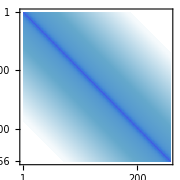

```mathematica
vsize=256;
{spaceconstant,maxstrength}={5.,0.05};
W=Table[N[-maxstrength Exp[-Abs[i-j]/spaceconstant],1],{i,vsize},{j,vsize}];
e3 = Table[.4*UnitStep[x-vsize/2]+.1,{x,1,vsize }];
MatrixPlot[W,ImageSize->Small]
```

a) Given the above step input, e3, and weight matrix W ( i.e. the inhibitory weights for the recurrent network with self-inhibition), find the steady-state solution to the limulus equation,  f = Wprime. e3, by solving a set of simultaneous linear equations using the Inverse[] function that computes the inverse of a matrix.

Using ListStepPlot[ ] (instead of ListPlot), plot the solution f,  along with the input pattern corresponding to the step e3. Recall that there is a Mathematica  function, IdentityMatrix[]. Your final plot should look like this:

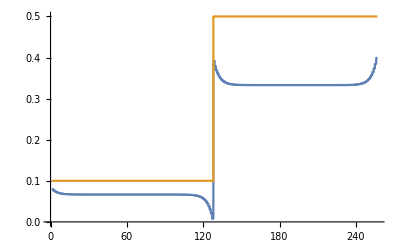

```mathematica
Wprime=Inverse[IdentityMatrix[Dimensions[W]]-W];
f = Wprime.e3;
ListStepPlot[{f, e3}]
```

b) How well does the linear lateral inhibition network predict what you see when looking at the region near a sharp vertical edge between the dark and light regions? Execute: Image[Table[e3,{256}]], and take a look. Ignore the boundary artifacts at the far left and right.

```mathematica
Image[Table[e3,{256}]]
```

-Graphics-

The linear lateral inhibition network predicts what I see pretty well, although the steepness of the curves near the vertical edge seems to exaggerate the phenomenon.

Convolution using ListConvolve[ ]

Convolution is perhaps the simplest example of a neural network architecture in which the same operation gets repeated over in space and/or time. It is a fundamental operation in models of image processing and recognition, as in “convolutional neural networks”. In terms of matrix construction, each subsequent row is equal to the previous row shifted right by one column width, together with boundary adjustments (e.g. one can wrap the row elements on the right back on to the left side, just terminate them, ...)

Let Wprime[[128]] be the vector corresponding to the 128th row of Wprime (from the previous exercise). Use ListConvolve[] and ListStepPlot[] to show that you get the same (or similar) output to the e3 stimulus as you obtained in the previous exercise. 

HINTS: One has to keep in mind the different ways to align the kernel, and handle extreme boundaries. 
	i) You can either align the kernel (i.e. Wprime) at position 128, but putting 128 as the third argument of ListConvolve; 
	Or, you can cyclically rotate the kernel using RotateRight[Wprime[[128]]], before doing the convolution, together with a maximal overhang at the left-hand end.
	ii) You only need one line of code -- just ListConvolve[ ] (with the correct variable settings) and ListStepPlot[].

Your output should look like this:

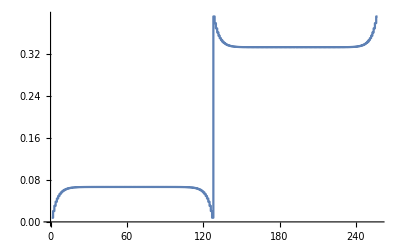

```mathematica
ListStepPlot[ListConvolve[Wprime[[128]], e3, 128]]
```

(Don’t worry if  the far left and/or right boundaries don’t match what you found in the previous exercise).

The Convolution Theorem. (Easy exercise, deep concept.) Confirm that convolution is equivalent to taking the inverse Fourier transform of the product of the Fourier transforms of the kernel and signal by executing this next line: ListStepPlot[Chop@InverseFourier[Fourier[WprimeR]*Fourier[e3]] Sqrt[Dimensions[e3][[1]]]]. This is an illustration of a famous Convolution Theorem. The Chop[] function is a quick way of removing tiny numerical errors.

Your output should look identical to the output of the previous exercise.

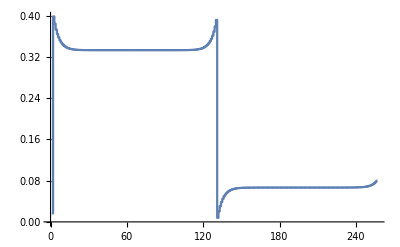

```mathematica
ListStepPlot[(Chop@InverseFourier[Fourier[Wprime]*Fourier[e3]] Sqrt[Dimensions[e3][[1]]])[[1]]]
```

Is the collection of row vectors in the basis set defined in the cell below linearly independent?

Execute the invisible cell below to initialize the matrix basisset.  
(On the desktop version of Mathematica, but apparently not on the cloud version, you can see what is in the cell by selecting the menu item: Cell:Cell Properties:Open).

```mathematica
basisset={{0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687},{0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687},{0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687},{0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687},{0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687},{0.35355339059327373,0.,0.,0.35355339059327373,0.,0.35355339059327373,0.35355339059327373,0.,0.35355339059327373,0.,0.,0.35355339059327373,0.,0.35355339059327373,0.35355339059327373,0.,-0.35355339059327373,0.,0.,-0.35355339059327373,0.,-0.35355339059327373,-0.35355339059327373,0.,-0.35355339059327373,0.,0.,-0.35355339059327373,0.,-0.35355339059327373,-0.35355339059327373,0.},{0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687},{0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687},{0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687},{0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687},{0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687},{0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687},{0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687},{0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687},{0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687},{0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687},{0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687},{0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687},{0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687},{0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687},{0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687},{0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687},{0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687},{0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687},{0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687},{0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687},{0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687},{0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687},{0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687},{0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687},{0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687},{0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687,0.17677669529663687,-0.17677669529663687}};
```

```mathematica
Inverse[Transpose[basisset]];
Inverse[basisset];
```

Inverse::sing: Matrix {{0.176777,0.176777,0.176777,0.176777,0.176777,0.353553,0.176777,0.176777,0.176777,0.176777,«22»},{0.176777,0.176777,0.176777,0.176777,0.176777,0.,0.176777,0.176777,0.176777,0.176777,«22»},«8»,«22»} is singular.

Inverse::sing: Matrix {{0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,«22»},{0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,«22»},«8»,«22»} is singular.

Neither the row vectors nor the column vectors in basisset are linearly independent. Neither basisset nor its inverse is invertible (they are singular).

Eigenvector property of a linear convolutional network

```mathematica
Clear[W,weights];
```

Let the weights to a single neuron be represented by the first row of a matrix W. We model the weights as a 1D  “gabor function”:

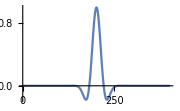

```mathematica
weights = Table[Cos[8. x] Exp[-(x*4.)^2],{x,-2,2,.01}];
ListPlot[weights,Joined->True,PlotRange->All,ImageSize->Small]
```

We want to construct W by inserting the weights vector in the first row, then again in the second row but shifted right by one, and so forth. This again captures the idea that each neuron prefers the same feature, but is looking for that feature at a different location.

To simplify dealing with how to introduce new elements on the left with each shift, we’ll wrap the right part of each gabor vector around to the left. If the kernel size is big, i.e. close to the number of columns, this is a bad way to deal with the boundary. However, for small kernels it isn’t too bad. ToeplitzMatrix[] constructs W with wrap-around automatically for us:

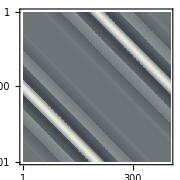

```mathematica
W = ToeplitzMatrix[weights];
MatrixPlot[W,ColorFunction->"GrayTones",ImageSize->Small]
```

a) Use ListPlot[,Joined->True] to plot the fourth eigenvector  of W. Note that the eigenvector is close to a sinusoidal form. The eigenvector property is the reason that sinusoids are particularly useful as test basis sets in linear systems analysis, especially when the network represents a shift-invariant invariant system , and correspondingly has a convolutional architecture. A sinusoid in produces a sinusoid out.

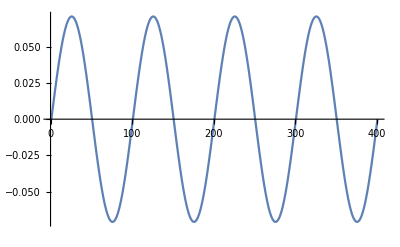

```mathematica
ListPlot[Eigenvectors[W][[4]], Joined->True]
```

b) Multiply the fourth eigenvector by W and then use CosineDistance[ ]  to verify that the resulting output vector points in the same direction as the input. You may not get the exact answer you expect, but you should be close.

```mathematica
CosineDistance[Eigenvectors[W][[4]].W, Eigenvectors[W][[4]]] (* Small cosine distance => about the same direction *)
```

2.69197×10^-31